```mathematica
Solve[E^x+Sin[x]=0,x]
```

Set::write: Tag Plus in ⅇ^x+Sin[x] is Protected.

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Solve[0,x]

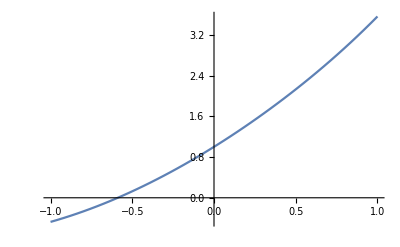

```mathematica
Plot[E^x+Sin[x],{x,-1,1}]
```

```mathematica
FindRoot[E^x+Sin[x],{x,-0.6}]
```

{x→-0.588533}

```mathematica
Reduce[x^2-5x+1>0,x]
```

x<1/2 (5-√21)||x>1/2 (5+√21)

```mathematica
f[x_]=(x^3-5x^2+3x+1)/(2x^2+x-1)
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
g[x_]=Log[(x^2-1)/(2x-3)]
```

Log[(-1+x^2)/(-3+2 x)]

```mathematica
h[x_]=Sin[x/3]-Cos[x^3/5]
```

-Cos[x^3/5]+Sin[x/3]

```mathematica
Solve[f[x]==0,x]
```

{{}}

```mathematica
Clear [f]
```

```mathematica
Reduce[f[x]>0,x]
```

-1<x<2-√5||1/2<x<1||x>2+√5

```mathematica
Reduce[f'[x]>0,x]
```

x<Root-3.38Root[1-#1+3 #1^2+#1^3&,1]-3.3829757679062373||x>2

```mathematica
N[%]
```

x<-3.38298||x>2.

```mathematica
FunctionDomain[g[x],x]
```

-1<x<1||x>3/2

```mathematica
Reduce[(X^2-1)/(2x-3)>0,x]
```

(X<-1&&x>3/2)||(-1<X<1&&x<3/2)||(X>1&&x>3/2)

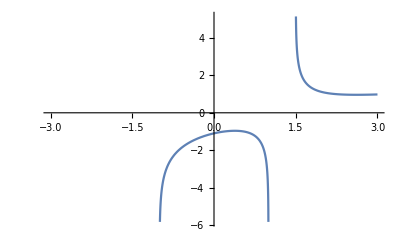

```mathematica
Plot[g[x],{x,-3,3}]
```

```mathematica
Solve[g'[x]==0,x]
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

```mathematica
g''[1/2 (3-√5)]
```

(√5 (3-√5) (-(3-√5)/(√5)-2/5 (-1+1/4 (3-√5)^2)))/((-1+1/4 (3-√5)^2)^2)+(2 (-(3-√5)/(√5)-2/5 (-1+1/4 (3-√5)^2)))/(-1+1/4 (3-√5)^2)-(√5 (-2/(√5)-4/5 (3-√5)-(8 (-1+1/4 (3-√5)^2))/(5 √5)))/(-1+1/4 (3-√5)^2)

```mathematica
N[%]
```

-2.34164

```mathematica
g[1/2 (3-√5)]
```

Log[-(-1+1/4 (3-√5)^2)/(√5)]

```mathematica
Simplify[%]
```

Log[1/2 (3-√5)]

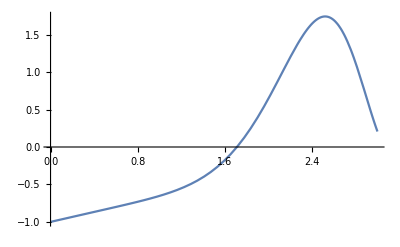

```mathematica
Plot [h[x],{x, 0, 3}]
```

```mathematica
Solve[h'[x]==0]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0]

```mathematica
NSolve[h'[x]==0]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0]

```mathematica
FindRoot[h'[x],{x,2.5},WorkingPrecision->10]
```

{x→2.519849493}